```mathematica
Play[Sin[500 t^5],{t,0,5}]
```

-Graphics-

```mathematica
EmitSound[%]
```

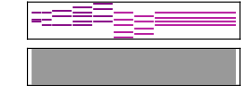

```mathematica
Sound[{SoundNote[{"D","Eb", "G"},.5,"Piano"],SoundNote[{"C","Eb", "G"},.5,"Piano"],
SoundNote[{"F","Ab", "C"},1,"Piano"],
SoundNote[{"C","D","F","Bb", "G"},1,"Piano"],
SoundNote[{"D4","F4","A4","C5"},1,"Piano"],
SoundNote[{"F3","Ab3","C4","Eb4", "G4"},1,"Harpsichord"],
SoundNote[{"G3","Bb3","D4", "F4"},1,"Harpsichord"],
SoundNote[{"C","D", "E", "G"},4,"Harpsichord"]}]
```

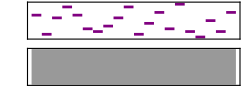

```mathematica
Sound[SoundNote /@ RandomInteger[12, 20], 5]
```

```mathematica
Button["press me",Speak["Yes indeed! You pressed me!"]]
```

press me

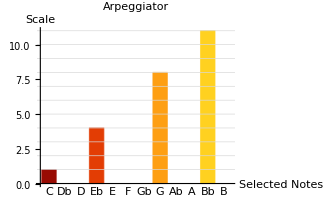

```mathematica
(* NOTE: Module needs a dummy input param. Why? *)
myArpeggiator[]:=
Module[{},
theNote = 1;
theCounter = 0;
currentNote = 0;
oldCurrentNote = 0;
voltRange = Range[0, 5, 0.05];
theResult = ConstantArray[0,12];
selectedNotes = {1,0,0,1,0,0,0,1,0,0,1,0};
oneStep = 5 / 12; (* MAX_VOLTAGE / SEMITONES_IN_OCTAVE *)

For [theCounter = 1, theCounter <= Length[voltRange], theCounter++,
{
currentNote=Ceiling[voltRange[[theCounter]]/oneStep];
If [(oldCurrentNote != currentNote),
{
If [selectedNotes[[currentNote]] == 1 ,
theResult[[theNote]] = currentNote;
];
 theNote = theNote + 1;
}
];
oldCurrentNote = currentNote;
}
];
theResult
];

(* Create bar chart from module. NOTE: Dummy value needed here. *)BarChart[myArpeggiator[], AxesLabel->{"Selected Notes", "Scale"},
GridLines->{None, Range[1,12]},
PlotLabel->"Arpeggiator", GridLinesStyle->LightGray,
ChartStyle->{Red,Green,Blue},
ColorFunction->ColorData["SolarColors"],
ChartLabels->{"C", "Db", "D", "Eb", "E", "F", "Gb", "G", "Ab", "A", "Bb", "B"}]
(* Calling module. *)
```

{1,4,8,11}

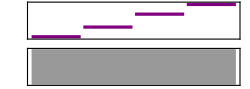

```mathematica
arpData = DeleteCases[myArpeggiator[], 0]
Sound[SoundNote /@ arpData,  2]
```

```mathematica
Play[Sin[5000t],{t,0,.1}]
```

-Graphics-

```mathematica
EmitSound[Play[Sin[5000t],{t,0,.1}]]
```